## Load data

```mathematica
SetDirectory@NotebookDirectory[];
data=Import["supplementary_data.xlsx"];
docs=data[[3]]; (*COLUMN NAMES: {"id","original","place","Latitude","Longitude","year","month","other","vydavatel","vydavatel2"}*)
docs[[2;;All,5]]=Round@docs[[2;;All,5]]; (*round years*)
docList=docs[[2;;All,1]]; (* document names only *)
issuerList=Union[docs[[2;;All,-2]]];  (* issuer names only *)
yearList=Union[docs[[2;;All,5]]];
missing={#,0}&/@Complement[Range[yearList[[1]],yearList[[-1]]],yearList];
(* years without any documents *)
funcList=data[[6,2;;All]]; (* function names only *)

incid=data[[4]]/.""->0;
names=DeleteCases[Drop[incid[[All,2]],1],0];
incid=incid[[2;;Length@names+1,Flatten[Position[incid[[1]],#]&/@docList]]];(* Same ordering as in docs *)
incidFunc=incid;
incid=incid/._String->1;
incid=SparseArray[incid,{Length@names,Length@docList}];
```

### Functions

```mathematica
makeNet[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]].Transpose[incid[[All,selectPos]]]-SparseArray@IdentityMatrix[Length[names]],Automatic,0]; (* make adjacency from incidence matrix *)
adjNam=DeleteCases[adjNam,PatternSequence[{x_,x_}->_]];
AppendTo[adjNam,{_,_}->∞];
g=WeightedAdjacencyGraph[SparseArray[adjNam,Length[names]]];
{adjNam,g}
];
```

```mathematica
(* This one takes some time *)
nets=ParallelTable[makeNet[year,year],{year,yearList}];
```

### Make networks

```mathematica
wholeNet=makeNet[yearList[[1]],yearList[[-1]]];
nn=VertexCount[wholeNet[[2]]];
ee=EdgeCount[wholeNet[[2]]];
```

### Graphics

```mathematica
marker1=Graphics[{EdgeForm[Directive[Thick,RGBColor[0,0,0],Opacity[1]]],White,Disk[]},ImageSize->14];
marker2=Graphics[{EdgeForm[Directive[Thick,RGBColor[1,0,0],Opacity[1]]],RGBColor[1,1,1],Triangle[{{0,0},{1,0},{1/2,√3/2}}]},ImageSize->15];
marker3=Graphics[{RGBColor[0,0,1],Polygon[{{1/2,0},{0,1/2},{1/2,1},{1,1/2}}]},ImageSize->15];
```

```mathematica
colors={Directive[(*Green*)RGBColor[0.34398, 0.49112, 0.89936],Thick],Directive[(*Blue*)RGBColor[0.97, 0.606, 0.081],(*Dashing[0.015],*)Thick](*Directive[Black,Thick]*),Directive[(*Black*)RGBColor[0.09096, 0.6296, 0.85532],Thick,DotDashed],Directive[(*Blue*)RGBColor[0.448, 0.69232, 0.1538],Dashing[0.03],Thick],Directive[(*Red*)RGBColor[0.62168, 0.2798, 0.6914],Thick,Dashing[0.015]],Directive[(*Red*)RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],Thickness[0.02]]};
```

```mathematica
(* Overlays for the timeline figures *)
shade=ListPlot[Transpose@{{1248+7/12,1249+8/12},ConstantArray[ee,2]},Joined->True,Filling->Bottom,FillingStyle->Directive[Red,Opacity[0.5]]];
line=ListPlot[{{1230,ee},{1253,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
line1=ListPlot[{{1230+0.5,ee},{1253+0.5,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
```

## Simple statistics

### Issuers

```mathematica
Grid@Reverse@SortBy[Tally@Cases[docs,{_,_,_,_,year_,_,_,x_}:>x/;1243≤year≤ 1256],Last]
```

král [king] | 61
markrabí [margrave] | 40
šlechtic [nobleman] | 19
klérus [clergy] | 8
královna [queen] | 3
biskup [bishop] | 3
měšťan [burgher] | 1

```mathematica
Grid@Reverse@SortBy[Tally@Cases[docs,{_,_,_,_,year_,_,x_,_}:>x/;1243≤year≤ 1256],Last]
```

Přemysl II. | 73
Václav I. | 28
Kunhuta | 3
Reinher | 2
Oldřich Korutanský | 2
Bruno | 2
Bavor ze Strakonic | 2
Vítek z Hradce | 1
Vikard z Trnavy | 1
Smil z Lichtenburka | 1
Smil z Bílkova | 1
Robert | 1
Petr | 1
Pardus z Horky | 1
Otto | 1
olomoucká kapitula | 1
Markéta z Miroslavi | 1
Kuno z Kunšátu | 1
Konrád | 1
Jindřich ze Žitavy | 1
Jaroslav z Hořence | 1
Jan z Polné | 1
Fridrich z Chomutova | 1
Dionýsius | 1
Boček z Jaroslavic | 1
Berthold | 1
Beneš z Úvalna | 1
Beneš | 1
Alramus | 1
Adelheid | 1

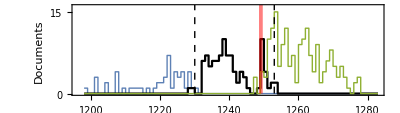

```mathematica
Show[{ListPlot[{Sort[Transpose[{yearList,Length@Position[docs,{__,#,_,"Přemysl I.",_}]&/@yearList}]~Join~missing],Sort[Transpose[{yearList,Length@Position[docs,{__,#,_,"Václav I.",_}]&/@yearList}]~Join~missing],Sort[Transpose[{yearList,Length@Position[docs,{__,#,_,"Přemysl II.",_}]&/@yearList}]~Join~missing]},Joined->True,InterpolationOrder->0,PlotStyle->{Directive[Automatic,Thick],Black},PlotLegends->Placed[LineLegend[{"Přemysl I","Wenceslas I","Přemysl Otakar"},LegendLabel->"Issuer:"],{0.15,0.65}],
Frame->True,PlotRange->{0,16},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],
FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,20,5}](*~Join~{{12,Style["4000",White],0}}*),Table[{t,"",{0.01,0}},{t,0,20,5}]},{Table[{t,t,{0.01,0}},{t,1200,1280,20}]~Join~Table[{t,"",{0.005,0}},{t,1200,1280,5}],Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["Documents","Arial",14,Black]},ImageSize->Automatic->460,AspectRatio->1/3.5],shade,line}]
```

### Distributions of signatures and signees

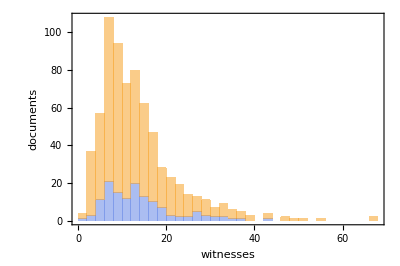

```mathematica
Histogram[{Total@incid[[All,Flatten[Position[docList,#]&/@Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;1243≤year≤ 1256]]]],Total@incid},PlotRange->All,ChartStyle->(Directive[EdgeForm[None],#]&/@colors[[1;;2]]),ChartLayout->"Stacked",Frame->True,AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,100,20}]~Join~Table[{t,"",{0.005,0}},{t,0,100,10}],Table[{t,"",{0.01,0}},{t,0,100,20}]~Join~Table[{t,"",{0.005,0}},{t,0,100,10}]},{Table[{t,t,{0.01,0}},{t,0,70,20}]~Join~Table[{t,"",{0.005,0}},{t,0,70,5}],Table[{t,"",{0.01,0}},{t,0,70,20}]~Join~Table[{t,"",{0.005,0}},{t,0,70,5}]}},FrameLabel->{Style["witnesses","Arial",12,Black],Style["documents","Arial",14,Black]},ImageSize->505/2,AspectRatio->2/3]
```

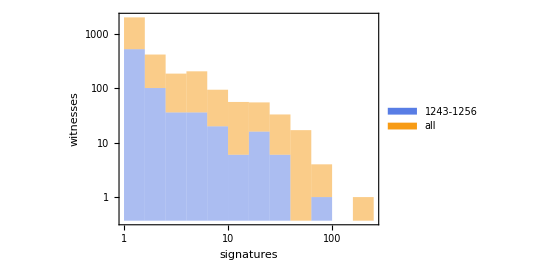

```mathematica
Histogram[{Total@Transpose@incid[[All,Flatten[Position[docList,#]&/@Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;1243≤year≤ 1256]]]],Total@Transpose@incid},{"Log",Automatic},"LogCount",PlotRange->All,ChartStyle->(Directive[EdgeForm[None],#]&/@colors[[1;;2]]),ChartLayout->"Stacked",Frame->True, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->Automatic,FrameLabel->{Style["signatures","Arial",12,Black],Style["witnesses","Arial",14,Black]},ImageSize->505/2,AspectRatio->2/3,ChartLegends->Placed[
SwatchLegend[colors[[1;;2]],(Style[#,FontFamily->"Arial",12,Black]&/@{"1243-1256","all"}),Spacings->.3],{.75,.75}]]
```

### Distributions of vertex degrees

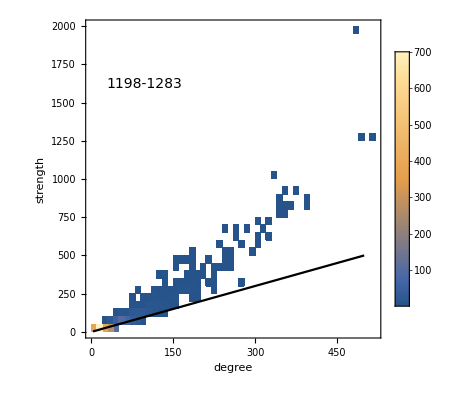

```mathematica
adj=SparseArray[Drop[wholeNet[[1]],-1]];
degs=DegreeCentrality[wholeNet[[2]]];
Show[
DensityHistogram[Transpose@{degs,Total[adj]},50,(*{"Log","Wand"},*)Frame->True,ChartLegends->Automatic,ImageSize->Automatic->250,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameLabel->(Style[#,14,"Arial",Black]&/@{"degree","strength"}),AspectRatio->1,
Epilog->Inset[(Style["1198-1283",FontFamily->"Arial",14,Black]),Scaled@{.2,.8}]]
,
(*LogLog*)Plot[{x(*,x^1.2*)},{x,3,500},PlotStyle->Black]
]
```

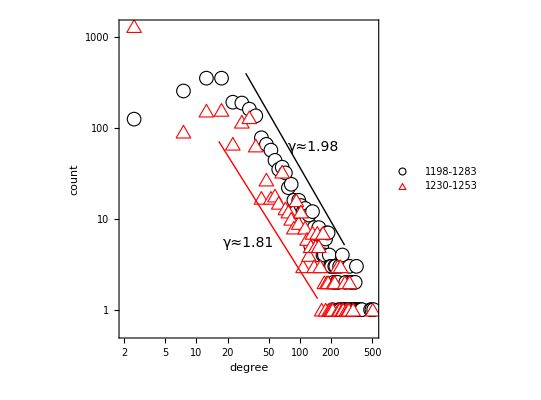

```mathematica
tail1=HistogramList[DegreeCentrality@wholeNet[[2]]];
tail2=HistogramList[DegreeCentrality@makeNet[1230,1253][[2]]];
tail1Fit=LinearModelFit[Log@Drop[DeleteCases[
Transpose[{MovingAverage[tail1[[1]],2],tail1[[2]]}],{_,0}
],3],{ x},x];
tail2Fit=LinearModelFit[Log@Drop[
DeleteCases[
Transpose[{MovingAverage[tail2[[1]],2],tail2[[2]]}],{_,0}
],3],{ x},x];
Show[
{
ListLogLogPlot[
{Transpose[{MovingAverage[tail1[[1]],2],tail1[[2]]}],Transpose[{MovingAverage[tail2[[1]],2],tail2[[2]]}]},
PlotLegends->Placed[(Style[#,FontFamily->"Arial",14,Black]&/@{"1198-1283","1230-1253"}),{.15,.15}],
PlotMarkers->{marker1,marker2},
Frame->True,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameLabel->(Style[#,14,"Arial",Black]&/@{"degree","count"}),
Epilog->{Inset[Style["γ≈"<>ToString@SetPrecision[-tail1Fit["BestFitParameters"][[2]],3],Black,"Arial",14],Scaled@{0.75,0.6}],Inset[Style["γ≈"<>ToString@SetPrecision[-tail2Fit["BestFitParameters"][[2]],3],Black,"Arial",14],Scaled@{0.5,0.3}]}],
Plot[{tail1Fit[x]+1},{x,3.4,5.6},PlotStyle->{Directive[Black,Thick]}],
Plot[{tail2Fit[x]-1},{x,2.8,5},PlotStyle->{Directive[Red,Thick]}]
},AspectRatio->1
]
```

### Reappearance of nodes and edges

```mathematica
counter=ConstantArray[0,nn];
Do[
temp=nets[[year]];
counter[[Union[Flatten@temp[[1,;;-2,1]]]]]+=1;
,{year,1,Length@yearList}];
reV=BinCounts[DeleteCases[counter,x_/;x<1]];
reV=Transpose@{Range[Length@reV-1],Drop[reV,1]};
```

```mathematica
counter=SparseArray[{_->0},{nn,nn}];
Do[
temp=nets[[year]];
(counter[[#[[1]],#[[2]]]]+=1)&/@Union[Sort/@temp[[1,;;-2,1]]];
,{year,1,Length@yearList}];
reE=BinCounts[DeleteCases[ArrayRules[counter][[;;-2,2]],x_/;x<1]];
reE=Transpose@{Range[Length@reE-1],Drop[reE,1]};
```

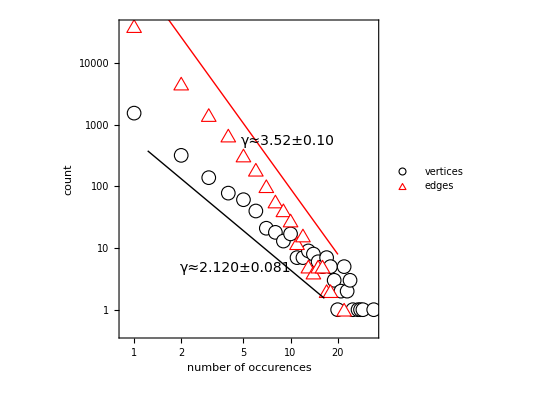

```mathematica
tail1Fit=LinearModelFit[Log@Drop[DeleteCases[reV,{_,0}],0],{ x},x];
tail2Fit=LinearModelFit[Log@Drop[DeleteCases[reE,{_,0}],0],{ x},x];
Show[
{
ListLogLogPlot[
{reV,reE},
PlotLegends->Placed[(Style[#,FontFamily->"Arial",14,Black]&/@{"vertices","edges"}),{.15,.15}],PlotMarkers->{marker1,marker2},
Frame->True,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameLabel->(Style[#,14,"Arial",Black]&/@{"number of occurences","count"}),
Epilog->{Inset[Style["γ≈"<>ToString@SetPrecision[-tail2Fit["BestFitParameters"][[2]],3]<>"±"<>ToString@SetPrecision[tail2Fit["ParameterErrors"][[2]],2],Black,"Arial",14],Scaled@{0.65,0.62}],Inset[Style["γ≈"<>ToString@SetPrecision[-tail1Fit["BestFitParameters"][[2]],4]<>"±"<>ToString@SetPrecision[tail1Fit["ParameterErrors"][[2]],2],Black,"Arial",14],Scaled@{0.45,0.22}]}],
Plot[{tail1Fit[x]-1},{x,.2,2.8},PlotStyle->{Directive[Black,Thick]}],
Plot[{tail2Fit[x]+1.5},{x,.5,3},PlotStyle->{Directive[Red,Thick]}]
},AspectRatio->1
]
```